```mathematica
d=Import["/home/cal/Documents/DSMC_Simulations/5_25_20_cold_second_stage/logs/dsmc_job_57432659.out","Table"];
```

```mathematica
rows=Cases[d,{a_,b_,c_,d_,e_,f_,g_,h_Integer}];
```

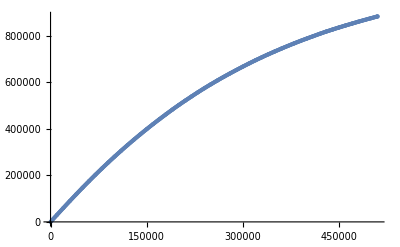

```mathematica
ListPlot[rows[[;;,{2,4}]],PlotRange->All]
```